```mathematica
Simplify[e3[q]^2-p3[q]^2]
```

m3^2

```mathematica
Simplify[e1[q,cos]*e2[q,cos]-p1z[q,cos]p2z[q,cos]-p1x[q,cos]p2x[q,cos]-p1p2[q]]
```

0.

```mathematica
Simplify[mqcos[q,cos]-mxme2[q,cos]]
```

0.

```mathematica
Simplify[m^4 (0.125+cos^2 (-0.125+(0.5 me^2)/q^2))+m3^4 (0.125-0.125 cos^2+(0.5 cos^2 me^2)/q^2)+0.5 cos^2 me^2 q^2+0.125 q^4-0.125 cos^2 q^4+m3^2 (-1. cos^2 me^2-0.25 q^2+0.25 cos^2 q^2)+m^2 (-1. cos^2 me^2+m3^2 (-0.25+cos^2 (0.25-(1. me^2)/q^2))-0.25 q^2+0.25 cos^2 q^2)]
```

m^4 (0.125+cos^2 (-0.125+(0.5 me^2)/q^2))+m3^4 (0.125+cos^2 (-0.125+(0.5 me^2)/q^2))+0.5 cos^2 me^2 q^2+0.125 q^4-0.125 cos^2 q^4+m3^2 (-0.25 q^2+cos^2 (-1. me^2+0.25 q^2))+m^2 (m3^2 (-0.25+cos^2 (0.25-(1. me^2)/q^2))-0.25 q^2+cos^2 (-1. me^2+0.25 q^2))

```mathematica
Simplify[p3p1[q,cos]]
Simplify[p3p2[q,cos]]
Simplify[2 p3p1[q,cos] p3p2[q,cos]]
```

(m^2 q-m3^2 q-q^3+cos √(-4 me^2+q^2) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))/(4 q)

-(-m^2 q+m3^2 q+q^3+cos √(-4 me^2+q^2) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))/(4 q)

1/(8 q^2)(-m^2 q+m3^2 q+q^3-cos √(-4 me^2+q^2) √((m^2-(m3-q)^2) (m^2-(m3+q)^2))) (-m^2 q+m3^2 q+q^3+cos √(-4 me^2+q^2) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))

```mathematica
temp[q_,cos_]:=1/(8 q^2)(q^2(-m^2 +m3^2 +q^2)^2-cos^2 (q^2-4 me^2)(m^2-(m3-q)^2) (m^2-(m3+q)^2) );
```

```mathematica
Simplify[Simplify[temp[q,cos]-m3^2 q^2/2]]
```

((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(8 q^2)

```mathematica
Integrate[Simplify[temp[q,cos]-m3^2 q^2/2],{cos,-1,1}]
```

((m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) (2 me^2+q^2))/(6 q^2)

```mathematica
m^2 Mee2[q,cos]
```

((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(4 q^2)

```mathematica
Simplify[p3p1[q,cos]]
```

(m^2 q-m3^2 q-q^3+cos √(-4 me^2+q^2) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))/(4 q)

```mathematica
Simplify[p3p1[q,cos]]
Simplify[p3p2[q,cos]]
Simplify[p3p1[q,cos]]
Simplify[p3p1[q,cos]p3p2[q,cos]]
```

(m^2 q-m3^2 q-q^3+cos √(-4 me^2+q^2) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))/(4 q)

-(-m^2 q+m3^2 q+q^3+cos √(-4 me^2+q^2) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))/(4 q)

(m^2 q-m3^2 q-q^3+cos √(-4 me^2+q^2) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))/(4 q)

1/(16 q^2)(-m^2 q+m3^2 q+q^3-cos √(-4 me^2+q^2) √((m^2-(m3-q)^2) (m^2-(m3+q)^2))) (-m^2 q+m3^2 q+q^3+cos √(-4 me^2+q^2) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))

```mathematica
Simplify[(m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) ]
```

(m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q)

```mathematica
Simplify[(m^2-2 m m3+m3^2-q^2)( m^2+2 m m3 +m3^2  -q^2)]
```

```mathematica
Simplify[(m^2-2 m m3+m3^2-q^2) (m^2+2 m m3+m3^2-q^2)]
```

```mathematica
Simplify[(m^2-2 m m3+m3^2-q^2) (m^2+2 m m3+m3^2-q^2)-(m^4+(m3^2-q^2)^2-2m^2(m3^2+q^2))]
m
```

0.125+3.72529×10^-9 q^2

3747.59

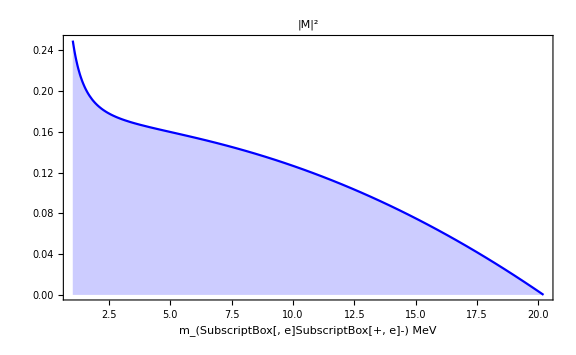

2.15214

```mathematica
n2=NIntegrate[me2[qq]/(m^2-m3^2)^2,{qq,qmin,qmax}];
Plot[me2[q]/(m^2-m3^2)^2,                   {q,qmin,qmax},
PlotLabel->"|M|^2",
Frame ->True, FrameLabel->{"m_(SubscriptBox[, e]SubscriptBox[+, e]-)   MeV"," "},
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,

PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
n2
```

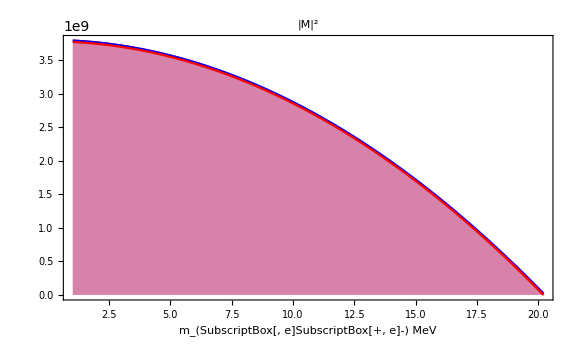

3747.59

```mathematica
m=mhe4s;
m3=mhe4;
me=0.51099907;
dm=m-m3;
me=me*1;
m1=me;

Plot[{mxmel02i[q],((m^2-m3^2)^2-4*m3^2*q^2)/6,m3^2*(dm^2-q^2)*2/3},                   {q,qmin,qmax},
PlotLabel->"|M|^2",
Frame ->True, FrameLabel->{"m_(SubscriptBox[, e]SubscriptBox[+, e]-)   MeV"," "},
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,

PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
m
```

```mathematica
Clear[m,m3,me];
Simplify[Integrate[mxmel002[q,cos],{cos,-1,1}]]
```

2/3 m^2 ((m-m3)^2-q^2)